# The Metric Tensor

Can graph distances recover the angular information of a metric tensor? We construct a dimensionless projection observable and compare it across scales. The square grid gives an exact example of scale consistency, though its limiting geometry retains the grid's preferred directions.

```mathematica
Needs[ "WolframInstitute`InfraGeometry`" ]
```

## Projection from graph distances

Fix a vertex p in a connected unweighted graph and an integer radius r>0. Write S_r(p)=={v:d(p,v)==r} for its shell and

I(p,w)=={x:d(p,x)+d(x,w)==d(p,w)}

for the vertices on shortest paths from p to w. For v,w∈S_r(p), let F(v,w) be the vertices of I(p,w) closest to v. We use the mean distance of these feet from the base:

T_r(v,w)==1/(r |F(v,w)|)∑_(x∈F(v,w)) d(p,x).

Thus 0≤T_r(v,w)≤1 and T_r(v,v)==1. InfraMetricTensor computes this table with "SelectCoordinate" -> Mean. Its default selector is Min; Max gives the other extreme when feet are tied. Rows and columns follow the sorted shell vertices.

A germ is one shortest path of length r starting at p. The collection of germs is the pencil at that scale. Projecting onto one germ gives a path-dependent observable; projecting onto I(p,w) uses all shortest paths with endpoint w. The metric tables below use the interval definition above.

The next grid compares a square lattice, square mesh and cube mesh above, and a sphere mesh, square torus and Sierpinski triangle below. The shell is gray, the interval from the centre red, and the probe blue. Orange marks its closest feet and one shortest path to a foot. The endpoint is the first shell vertex; the probe is another shell vertex whose distance from it is closest to r. These choices use graph distances alone, so the same construction applies to every substrate.

```mathematica
GraphicsGrid[
  Partition[
    Table[
      With[
        { g = BlockRandom[ InfraSubstrate[ specification[[ 1 ]], "Large" ], RandomSeeding -> 2 ] },
        { p = First @ GraphCenter[ g ], distances = GraphDistanceMatrix[ g ] },
        { r = Floor[ GraphRadius[ g ] / 2 ] },
        { shell = Keys @ InfraMeasurement[ g, InfraShell[ p, r ], "VertexDensity" ] },
        { w = First[ shell ] },
        { probe = First @ MinimalBy[ Select[ shell, vertex |-> vertex =!= w ],
            vertex |-> Abs[ distances[[ VertexIndex[ g, w ], VertexIndex[ g, vertex ] ]] - r ] ],
          interval = Keys @ InfraMeasurement[ g, InfraSegment[ p, w ], "VertexDensity" ] },
        { feet = MinimalBy[ interval,
            vertex |-> distances[[ VertexIndex[ g, vertex ], VertexIndex[ g, probe ] ]] ] },
        { connector = First @ RandomInfraSegment[ g, InfraSegment[ probe, First[ feet ] ], 1, RandomSeeding -> 1 ] },
        Labeled[
          InfraSubstrateHighlight[ g, {
            shell -> StandardGray, InfraSegment[ p, w ] -> StandardRed,
            InfraWalk[ connector ] -> StandardOrange, feet -> StandardOrange, { p, w, probe } -> StandardBlue } ,
            "ThicknessRange" -> { 1.25, 5 } ],
          specification[[ 2 ]] ] ],
      { specification, {
          { "SquareTilingGraph", "square lattice" }, { "SquareMeshGraph", "square mesh" },
          { "CubeMeshGraph", "cube mesh" }, { "SphereMeshGraph", "sphere mesh" },
          { "SquareTorusGraph", "square torus" }, { "SierpinskiTriangleGraph", "Sierpinski triangle" } } } ],
    3 ],
  ImageSize -> 1200 ]
```

-Graphics-

In the Euclidean plane, put v==ra and w==rb for unit vectors a,b. A point of [0,w] has the form tb, with 0≤t≤r, and

∥ra-tb∥^2==r^2+t^2-2rt(a·b).

The minimizing parameter is t==rmax(a·b,0), so the reference value is max(cosθ,0). This is only the positive projection part of the Euclidean inner product. At finite graph scale, symmetry and bilinearity are not automatic, and the pencil has no specified vector-space operations.

## One germ against the pencil

The color runs along one germ from blue at the base, through yellow, to red at its endpoint. Each shell vertex takes the color of the parameter where the germ comes closest to it, averaged over ties and divided by r. This picture uses projection onto the displayed path; the metric tables use projection onto the whole interval. The columns are square and triangular tilings and an irregular mesh; the rows are medium and large substrates.

```mathematica
GraphicsGrid[
  Table[
    With[
      { g = BlockRandom[ InfraSubstrate[ name, size ], RandomSeeding -> 2 ] },
      { p = First @ GraphCenter[ g ], distances = GraphDistanceMatrix[ g ] },
      { r = Floor[ GraphRadius[ g ] / 2 ] },
      { shell = Keys @ InfraMeasurement[ g, InfraShell[ p, r ], "VertexDensity" ] },
      { germ = First @ RandomInfraSegment[ g, InfraSegment[ p, First[ shell ] ], 1, RandomSeeding -> 1 ] },
      { indices = Map[ vertex |-> VertexIndex[ g, vertex ], germ ] },
      { parameters = AssociationThread[ shell,
          Map[ endpoint |-> With[
            { alongGerm = distances[[ VertexIndex[ g, endpoint ], indices ]] },
            Mean @ Pick[ Range[ 0, r ], alongGerm, Min[ alongGerm ] ] ], shell ] / N[ r ] ] },
      { color = t |-> Blend[ { StandardBlue, StandardYellow, StandardRed }, t ] },
      Labeled[ InfraSubstrateHighlight[ g, Join[
        Table[ InfraWalk[ germ[[ k ;; k + 1 ]] ] -> color[ k / r ], { k, r } ],
        Map[ edge |-> InfraWalk[ List @@ edge ] -> color[ Mean[ parameters /@ ( List @@ edge ) ] ],
          Select[ EdgeList[ g ], edge |-> SubsetQ[ shell, List @@ edge ] ] ],
        KeyValueMap[ { t, vertices } |-> vertices -> color[ t ], GroupBy[ shell, parameters ] ],
        { { p } -> color[ 0 ] } ] ,
        "ThicknessRange" -> { 1.25, 5 } ],
        Row[ { StringReplace[ name, { "TilingGraph" -> " tiling", "MeshGraph" -> " mesh" } ], ", ", size } ] ] ],
    { size, { "Medium", "Large" } },
    { name, { "SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph" } } ],
  ImageSize -> 1200 ]
```

-Graphics-

## An exact comparison across scales

On the square grid, graph distance is the sum of the absolute coordinate differences. The interval I(p,w) is a coordinate rectangle. Its closest vertex to v is obtained by clamping each coordinate of v to that rectangle. After translating p to the origin, write z for the clamp of a coordinate u of v to the interval between 0 and the corresponding coordinate b of w. If ub≤0, then z==0 and Abs[u-b|==|u|+|b]. If ub≥0, then |z|==min(Abs[u|,|b]). In both cases, 2|z|==|u|+|b|-|u-b|. Summing over the two coordinates gives

d(p,F(v,w))==(d(p,v)+d(p,w)-d(v,w))/2,    T_r(v,w)==1-(d(v,w))/(2r).

Here the foot is unique. The next panels show the same configuration at r==6,12,24, with coordinates divided by r. The graph shell stays a diamond inside the dashed Euclidean unit circle. The red interval and orange projection keep their shape while the graph becomes finer.

```mathematica
GraphicsRow[
  Table[
    With[
      { coordinates = Tuples[ Range[ -r, r ], 2 ] },
      { g = GridGraph[ { 2 r + 1, 2 r + 1 }, VertexCoordinates -> coordinates / r,
          Sequence @@ InfraSubstrateStyle[ "Large" ] ],
        positions = Map[ point |-> First @ FirstPosition[ coordinates, point ],
          { { 0, 0 }, { r, 0 }, { r / 2, r / 2 }, { r / 2, 0 } } ] },
      { p = positions[[ 1 ]], w = positions[[ 2 ]], probe = positions[[ 3 ]], foot = positions[[ 4 ]] },
      Labeled[ InfraSubstrateHighlight[ g, {
        InfraShell[ p, r ] -> StandardGray, InfraSegment[ p, w ] -> StandardRed,
        InfraSegment[ probe, foot ] -> StandardOrange, { foot } -> StandardOrange,
        { p, w, probe } -> StandardBlue },
        Epilog -> { StandardGray, AbsoluteThickness[ 1.5 ],
          Line[ { { 1, 0 }, { 0, 1 }, { -1, 0 }, { 0, -1 }, { 1, 0 } } ],
          Dashed, Circle[ { 0, 0 }, 1 ] } ,
        "ThicknessRange" -> { 1.25, 5 } ], Row[ { "r = ", r, ", projection = 1/2" } ] ] ],
    { r, { 6, 12, 24 } } ],
  ImageSize -> 1000 ]
```

-Graphics-

Multiplying lattice coordinates and r by the same positive integer leaves the corresponding tensor entries unchanged. This is an exact scale consistency after measuring lengths in units of r.

It does not make the grid Euclidean. For p==(0,0), w==(r,0) and v==(r/2,r/2) with even r, the entry is always 1/2. The Euclidean angle between these directions is π/4, whose cosine is 1/√2. The discrepancy persists at every such scale because the rescaled graph metric remains the ℓ^1 metric.

## Seeing the projection table

The columns below are the large square tiling, triangular tiling and irregular mesh. The first row shows T_r; the second shows the clipped cosine between the same embedded directions. The third row subtracts the second from the first, using the same color scale in every panel: blue is negative, gray is zero and red is positive. This comparison retains the pairing of directions, which a distribution of table entries would discard. The embedding only orders directions and supplies the Euclidean comparison. Each shell is read at half the graph radius.

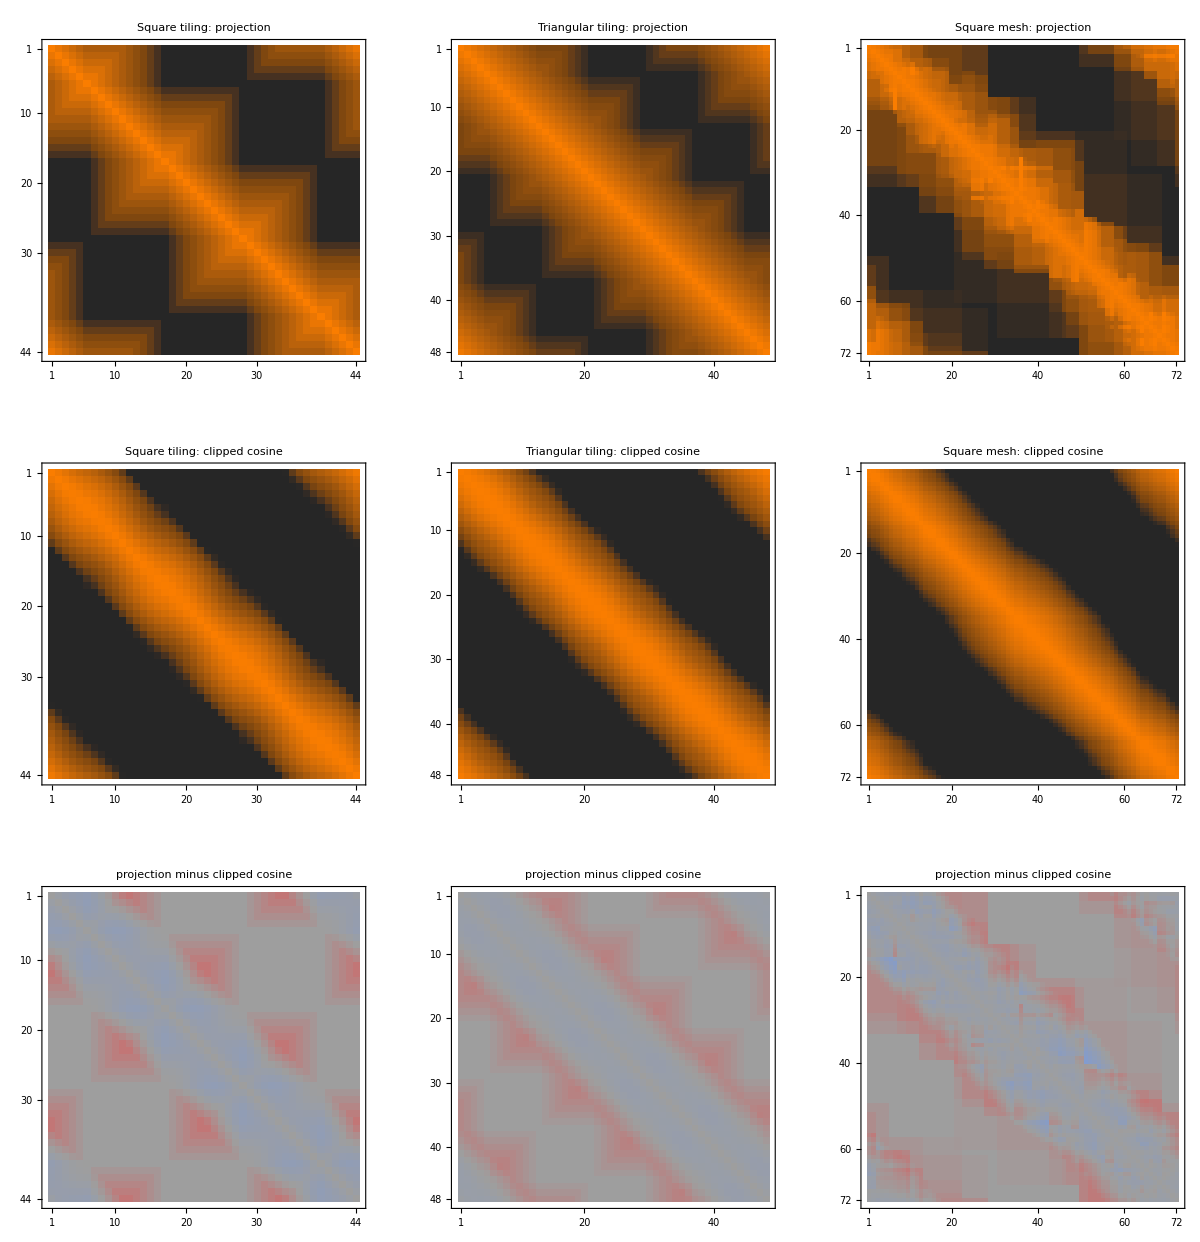

```mathematica
GraphicsGrid[ Transpose @ Table[
  With[
    { g = BlockRandom[
        InfraSubstrate[ name, "Large", "KeepCoordinates" -> True ], RandomSeeding -> 2 ] },
    { p = First @ GraphCenter[ g ], coordinates = AssociationThread[ VertexList[ g ], GraphEmbedding[ g ] ] },
    { r = Floor[ GraphRadius[ g ] / 2 ] },
    { shell = Sort @ Keys @ InfraMeasurement[ g, InfraShell[ p, r ], "VertexDensity" ] },
    { directions = Map[ v |-> Normalize[ coordinates[ v ] - coordinates[ p ] ], shell ],
      order = Ordering[ Map[ v |-> Mod[ ArcTan @@ ( coordinates[ v ] - coordinates[ p ] ), 2 Pi ], shell ] ] },
    { tensor = InfraMetricTensor[ g, p, r, "SelectCoordinate" -> Mean ],
      reference = Clip[ Outer[ Dot, directions, directions, 1 ], { 0, 1 } ] },
    Join[
      MapThread[
        { matrix, title } |-> MatrixPlot[ matrix[[ order, order ]], PlotRange -> { 0, 1 }, AspectRatio -> 1,
          PlotLabel -> Row[ {
            StringReplace[ name, { "TilingGraph" -> " tiling", "MeshGraph" -> " mesh" } ], ": ", title } ] ],
        { { tensor, reference }, { "projection", "clipped cosine" } } ],
      { MatrixPlot[ ( tensor - reference )[[ order, order ]], PlotRange -> { -1, 1 }, AspectRatio -> 1,
          ColorFunction -> ( t |-> Blend[ { StandardBlue, StandardGray, StandardRed }, ( t + 1 ) / 2 ] ),
          ColorFunctionScaling -> False, PlotLabel -> "projection minus clipped cosine" ] } ] ],
  { name, { "SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph" } } ], ImageSize -> 1200 ]
```

## Comparing distributions

For a comparison that needs no embedding, give every ordered pair of shell vertices equal weight. Let F_r be the distribution function of the resulting entries. Uniform directions in the Euclidean plane give the reference distribution

F(t)==1-arccost/π,    0≤t≤1,

including an atom of mass 1/2 at zero. We measure the discrepancy by

Δ_r==∫_0^1 |F_r(t)-F(t)|ⅆt.

The helper uses a midpoint approximation with step 0.001.

```mathematica
projectionGap[ values_ ] :=
  With[ { distribution = EmpiricalDistribution[ Flatten[ values ] ], grid = Range[ 0.0005, 0.9995, 0.001 ] },
    Mean @ Abs @ Map[ t |-> CDF[ distribution, t ] - ( 1 - ArcCos[ t ] / Pi ), grid ] ]
```

For each tiling, increase r inside one large patch. For the mesh, refine the graph and read the shell at half its graph radius. The two procedures share the normalization d/r, though they change the substrate in different ways.

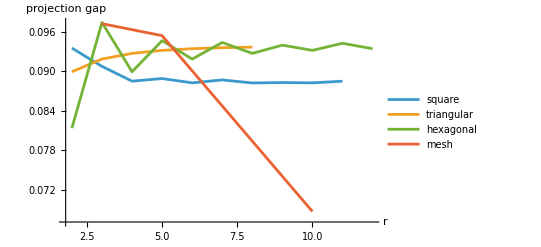

```mathematica
ListLinePlot[
  Join[
    Table[
      With[
        { g = InfraSubstrate[ name, "Large" ] },
        { p = First @ GraphCenter[ g ] },
        Table[ { r, projectionGap[ InfraMetricTensor[ g, p, r, "SelectCoordinate" -> Mean ] ] },
          { r, 2, Floor[ GraphRadius[ g ] / 2 ] } ] ],
      { name, { "SquareTilingGraph", "TriangularTilingGraph", "HexagonalTilingGraph" } } ],
    { Table[
        With[
          { g = BlockRandom[ InfraSubstrate[ "SquareMeshGraph", size ], RandomSeeding -> 2 ] },
          { p = First @ GraphCenter[ g ], r = Floor[ GraphRadius[ g ] / 2 ] },
          { r, projectionGap[ InfraMetricTensor[ g, p, r, "SelectCoordinate" -> Mean ] ] } ],
        { size, { "Small", "Medium", "Large" } } ] } ],
  PlotRange -> All, AxesLabel -> { "r", "projection gap" },
  PlotLegends -> { "square", "triangular", "hexagonal", "mesh" } ]
```

A stable nonzero gap can describe a scale-consistent geometry with persistent anisotropy. A decreasing gap is evidence for this particular Euclidean statistic. Even equality of value distributions would not identify which directions have which entries. A Euclidean limit requires compatible directions across scales and control of both the metric and the shell measure. Counting germs instead of shell vertices changes that measure, since some endpoints admit more shortest paths.

The Breathless Line gives a complementary example where normalized path occupation converges to a Euclidean segment even though the underlying grid metric remains anisotropic.

Related Guides

RiemannianInfrageometrypaclet:WolframInstitute/InfraGeometry/guide/RiemannianInfrageometry

Related Tech Notes

## Metadata

### Categorization

Tutorial

WolframInstitute/InfraGeometry

WolframInstitute`InfraGeometry`

WolframInstitute/InfraGeometry/tutorial/MetricTensorTutorial

### Keywords

metric tensor

projection

shell

cosine

scale consistency

lattice

mesh